# 筑波大学 知識構造化法 (2014~2016年) 抜粋・加筆記事

## 2.計算機とデータ構造について

われわれは膨大な知識を処理するために計算機に頼る。したがって知識は計算機にとっても利用可能でなくてはならないことを前提とする。

計算機にとってすべてはデータである。

### データとは

処理系が扱える表現全てがデータである。

ちなみに: CPU内の処理を考えるとき、「instruction」と「data」に分けて考える。ここでの「data」は良く定義された狭義の概念。

#### データ型

ほとんどすべての処理系やプログラミング言語では、データ型が定義されている（データそのものはバイト列にすぎない）。

基本的な型（ほぼどの言語も備えている）:

- 整数（Integer）

- 浮動小数（Real）

- ブール代数

- 文字

- ポインタ

上位構造（おもにユーザーが定義する）:

- 配列

-- ベクトル

-- 行列

-- テンソル

-- 文字列

- 複素数（Complex）

- 構造体

- 列挙型

- リスト（連結セル）

#### データ構造

- 計算機から見ればデータ型の組み合わせ。

- 利用者から見ればいわゆるデータフォーマット。

### 処理系とは

一般的には、OSおよびその上で動作するアプリケーションを指す。

### データ処理とは

データ処理とは、処理対象と処理命令の定義が記述された表現を、その表現以外の知識（ルール）を用い、表現が変化しなくなるまで評価を続けることである（べつの言葉で言えば、表現評価系を用いた表現の変換）。処理対象と処理命令は、分離が曖昧であり広い意味ではすべて処理対象である（何が対象で何が命令かはユーザーが決める）。

「計算機」と「データ」の概念はチューリングマシンのそれとおなじである。「人間からの割り込みを許すチューリングマシン」としての実装が「計算機」である。

「計算機」と「データ」の実体すなわち実装は（いまのところ）機械的および電磁気的な現象の操作・制御であり、「計算機」はこれを効率的に行い何らかの結果を人間に提示する仕組みである。

#### データ処理の抽象化 -> チューリングマシン

チューリングマシンとは
アラン・チューリングによる仮想機械とそのしくみ。計算機を抽象化したもの。

チューリングマシンの部品

機械（マシン）

マシンの状態を保持するメモリ

テープの状態を読み取るヘッド

無限に長いテープ

チューリングマシンの形式的要素

M: 機械の状態を表す有限集合

T: テープに記載される記号の有限集合

b: Tの元である空白記号

Σ: b以外のTの部分集合

δ: 遷移関数: δ(m,t)=(m’,t’,h): 機械の状態がm、テープの着目位置の記号がtのとき、機械の状態をm’に、テープの着目位置の記号をt’に変更したあと、テープの着目位置をh側に一つ移動。
ただし、

m: Mの元

t: Tの元

h: 次のステップでテープ上をどちらに動くか: {L,R}

mi: 初期状態(mi∈M)

ma: 受理状態(ma∈M)

黒板で説明 <- 手書きメモ

Mathemticaのチューリングマシン関数

```mathematica
??TuringMachine
```

RowBox[{"TuringMachine", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", StyleBox["t", "TI"]}], "]"}] 指定されたルールで初期条件 StyleBox["init", "TI"] から StyleBox["t", "TI"] ステップ進んだチューリングマシンの進化を表すリストを生成する． 
RowBox[{"TuringMachine", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"]}], "]"}] StyleBox["init", "TI"] を1ステップ進化させた結果を与える．

Attributes[TuringMachine]={Protected,ReadProtected}

s色-k色チューリングマシンのすべての状態:

```mathematica
turingCurrentState[s_,k_]:=Module[
{sets,setk,current},
sets=Range[0,s-1];
setk=Range[0,k-1];
current=Flatten[Outer[List,sets,setk],1]
]
```

上記状態に対応するルールすべて:

```mathematica
turingAllRules[s_,k_]:=Module[
{(*numrule,*)numStateSet,numOperateSet,sets,setk,(*current,*)selections,next},
(*numrule=(2 s k)^(s k);*)
numStateSet=s k;
numOperateSet=2 s k;
sets=Range[0,s-1];
setk=Range[0,k-1];
selections=Tuples[Range[numOperateSet],numStateSet];
next=Flatten[Outer[List,sets,setk,{"L","R"}],2];
Map[next[[#]]&,selections]
]
```

２色ヘッド-２色テープの場合の組み合わせ

```mathematica
turingCurrentState[2,2]
```

{{0,0},{0,1},{1,0},{1,1}}

２色ヘッド-２色テープの場合の組み合わせそれぞれに対して、{0/1,0/1,L/R}の8通りのルールを作ることができる。

第2506ルール

```mathematica
turingAllRules[2,2]//Length
```

4096

```mathematica
IntegerDigits[4095,2,12]
```

{1,1,1,1,1,1,1,1,1,1,1,1}

出力の読み方:
 {{<ヘッドの状態>,<”テープの状態表示”における先頭要素に対するヘッドの位置>,<初期状態からのヘッドの移動>},{<テープの状態表示>}}

```mathematica
TuringMachine[2506,{1,{{},0}},0]
```

{{{1,1,0},{0}}}

```mathematica
TuringMachine[2506,{1,{{},0}},2]//MatrixForm
```

({1,1,0} | {0,0}
{2,2,1} | {1,0}
{1,1,0} | {1,1})

```mathematica
TuringMachine[2506,{1,{{},0}},3]//MatrixForm
```

((1
2
0) | (0
0
0)
(2
3
1) | (0
1
0)
(1
2
0) | (0
1
1)
(2
1
-1) | (0
0
1))

ルールを切り替えながらturingmachineを継続するプログラム

```mathematica
turingNext[state_,rl_/;Depth[rl]==2]:=TuringMachine[rl[[1]],state[[-1]],rl[[2]]]
```

```mathematica
turingSequence[init_,rls_]:=Module[{seed,first},
seed=FoldList[turingNext,{init},rls];
first=seed[[1,1]];
Prepend[Apply[Join,Map[Drop[#,1]&,Drop[seed,1]]],first] ]
```

```mathematica
init={{1,1,0},{0}}
```

{{1,1,0},{0}}

```mathematica
turingSequence[init,{{2506,2},{2506,1}}]
```

{{{1,1,0},{0}},{{2,1,1},{1}},{{1,1,2},{0}},{{2,1,3},{1}}}

```mathematica
TuringMachine[2506,TuringMachine[2506,init,0][[-1]],3]
```

{{{1,1,0},{0}},{{2,1,1},{1}},{{1,1,2},{0}},{{2,1,3},{1}}}

```mathematica
TuringMachine[2506,init,3]
```

{{{1,1,0},{0}},{{2,1,1},{1}},{{1,1,2},{0}},{{2,1,3},{1}}}

#### データ処理の具体化 -> 物理的な機械（計算機）による動作

データ処理（計算）を行うことは、物理的には何らかの物理状態を（自動的かつ継続的に）変化させることである。

電子計算機においてはCPU内のレジスタの状態を変化させることに相当し、広い意味では記憶装置や表示装置を含む計算機の動作を指す。

CPU内のALUにより計算（演算）された結果は、一時的にレジスタに保持され、その結果はメインメモリにコピーされる。メインメモリ上のデータも揮発的であり、永続的に保存するにはストレージが必要である。

#### セルオートマトン（参考）

一方、局所規則のみで自己組織的に駆動する構造がセルオートマトンである。一部の規則群がチューリング完全である。つまり、適切な規則を定義することによりチューリングマシンとして機能する。

黒板で説明 <- 手書きメモ

1近傍d次元における第nルールを得る（<-Mathematicaの第nルールと合致しているかは未確認なので考え方のみ）:

```mathematica
numRuleToCellList[n_,d_]:=(* n: 第nルール、d: d次元 *)
Module[{dig,stats,box,bbox,cellstat},
dig=3^d;
stats=2^dig;
bbox=Reverse[Map[IntegerDigits[#,2,dig]&,Range[0,stats-1]]];
cellstat=IntegerDigits[n,2,stats];
Transpose[{bbox,cellstat}]
]
```

```mathematica
numRuleToCellList[1,1]
```

{{{1,1,1},0},{{1,1,0},0},{{1,0,1},0},{{1,0,0},0},{{0,1,1},0},{{0,1,0},0},{{0,0,1},0},{{0,0,0},1}}

1次元のルールを表で示す:

```mathematica
cellListVis1D[rule_]:=Grid[{Map[Grid[{#[[1]],{Null,#[[2]],Null}},Frame->All]&,rule]}]
```

1近傍、1次元、第0ルール:

```mathematica
cellListVis1D[numRuleToCellList[0,1]]
```

1 | 1 | 1
 | 0 |  | 1 | 1 | 0
 | 0 |  | 1 | 0 | 1
 | 0 |  | 1 | 0 | 0
 | 0 |  | 0 | 1 | 1
 | 0 |  | 0 | 1 | 0
 | 0 |  | 0 | 0 | 1
 | 0 |  | 0 | 0 | 0
 | 0 |

```mathematica
??CellularAutomaton
```

RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", StyleBox["t", "TI"]}], "]"}] 指定した条件でセルオートマトンを初期条件 StyleBox["init", "TI"] から StyleBox["t", "TI"] ステップ実行した進化を表すリストを生成する．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"]}], "]"}] 1ステップ分の StyleBox["init", "TI"] の進化の結果を返す．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["tspec", "TI"], ",", StyleBox["xspec", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] StyleBox["tspec", "TI"]，StyleBox[RowBox[{"xspec", " "}], "TI"]等で指定された進化の部分だけを返す．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["t", "TI"], ",", "All", ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] StyleBox["t", "TI"] ステップの間に影響を受けるであろうすべてのセルを各ステップに含む．

Attributes[CellularAutomaton]={Protected}

{0,0,0,1,0,0,0}に対してルール30を3ステップ実行する:

```mathematica
CellularAutomaton[30,{0,0,0,1,0,0,0},2]
```

{{0,0,0,1,0,0,0},{0,0,1,1,1,0,0},{0,1,1,0,0,1,0}}

可視化する:

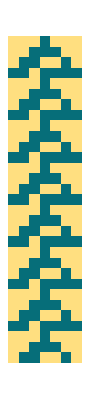

```mathematica
CellularAutomaton[30,{0,0,0,1,0,0,0},30]//ArrayPlot
```

#### ラムダ計算(今期やらない)

### プログラミング言語とは

（利用者が）データ処理をしやすくするための仕組みであり、広義には、人間が計算機へ指示（とくにバッチ処理）を伝えるための言語であるが、これではさまざまな仕組みがプログラミング言語になってしまう。

そこで、狭義には以下のように考えるのが適当。

コンパイラ（インタープリタ）に動作を解釈させるための言語である。

効率的にデータ処理を行うためにコンパイラ（インタープリタ）に必要とされる機能 :

抽象化（変数）
 ポインタもアドレスを格納する変数に過ぎない。

繰り返し（または再帰）
再帰表現と繰り返し表現は可換であるが、双方備えるべき。

条件分岐

### 知識（データ）の伝達と獲得

計算機 <-> 外界（人間含む）

計算機 <-> 計算機

#### いままでは、計算機上にすでにある情報（データ）を扱う話。では、外の世界の情報を計算機で扱うには? （計算機が外界の情報を手に入れる手段は?）

通信以外では、センサーを使う（センサーと接続可能な場合）。または、（センサーの）データを一般的なIOで読み込む。

Linuxにおけるマウスの例
 /dev/input/mouse1

MacではControllerInformation[]が使える

```mathematica
ControllerInformation[]
```

#### 計算機が他の計算機に知識を伝える手段は?

ネットワーク

P2P

## 11. 大規模データ解析と計算資源

大規模データの問題:
- 計算に時間がかかる
- データの保持とアクセスが難しい

### 計算資源

中央演算装置（CPU）

メインメモリー

ストレージ

各装置を接続するバスやブリッジ

外部通信装置

### 物理アクセスのレベル

計算（instruction）はCPU内の演算器で行われるので、演算器付近にデータがあるほど計算が速い。

情報は物理状態として保持され、情報伝達は物理状態変化によって行なわれるので、すべての情報間の距離をゼロにすることはできないし、その距離も一定ではない。このことは、効率のよい計算を行うには、複雑な情報伝達システムを設計しなければならないだけでなく、利用者もデータ保持の階層を意識する必要があることを意味する。

データ保持の階層 = CPU内の演算器からのアクセスのレベル:

- 演算器がレジスタ（どちらもCPU内にある）の値を処理することにより演算が行なわれる。->もっとも速いアクセス

- 計算に必要な情報がレジスタに無い場合、CPU内部キャッシュが検索される。-> 次に速いアクセス

- 計算に必要な情報が、さらに、外部キャッシュ -> メインメモリ（不均一アクセスあり:NUMA）　->　ストレージ、に存在する順にアクセスは遅くなる。

### コード解釈のタイプ

計算の実行は一般的に利用者のコードをコンパイルした後に行うが、いくつかの方法がある。一般的にコンパイル時間と実行時間はトレードオフとなる。

バイナリ
コンパイルによりOS上でそのまま実行できるファイルを作成。

スクリプト/インタープリタ
スクリプトを実行するプログラムが呼び出され、そのプログラムがスクリプトを解釈する（行ごとにコンパイル/実行するイメージ）。

VMコード
仮想マシンが呼び出され、仮想マシン上でコードが実行される。この限りにおいてはスクリプトファイルの実行と変わらないが、仮想マシンは万能チューリングマシンとして設計されているので、より柔軟な対応が可能となる。これにより、スクリプト言語風のプログラムコードの実行のパフォーマンスを、コンパイルされたバイナリのそれと同程度に向上させられる。一般的にソースをVM用にコンパイルして使う。

### 計算を速くするには

データ配置の工夫が必要で、これにはコンパイル（またはインタープリタ）が大きく関わる。 -> これは、効率化のためには問題に応じてユーザーがコンパイラやインタープリタ（つまりアプリ）を選ばないといけないということ。

- 演算器と必要なデータの距離を近くする（情報の配置を最適化する） -> メインメモリ<->レジスタ間に関してコンパイラはこれをやっている。

- 考えをさらに進めて計算機資源全体をより高度な方法で管理する -> VM（JAVAなど）はこれをやっている（JITコンパイル、TAC）。

- OSそのものが近代的なVMの機能を持てば、より効率は上がると考えられる。-> 実用的なシステムはまだない。

- 計算機を寄せ集めて使うこともデータ配置の工夫の一つ。-> 計算機クラスター。

-- 並列計算（マルチスレッド・マルチプロセス）

-- 平行計算（複数ジョブ同時実行）

- 現在の主流は、計算機クラスター上でコンパイルしたバイナリ（メッセージパッシング機能を含む）を使う。

### 現在の主流 -計算機クラスター + MPI + OMP + GPGPU + ジョブ管理システム-

計算機クラスター:
PCと同じような構成の、あるいは、より簡略（近年、インターコネクトがCPUに引き込まれ簡略ではなくなってきている）な構成の安価な計算ノードを、ネットワーク（この場合、とくにインターコネクトと言う）でつなぎ合わせる方式。

計算ノード:
計算ノードとは一般的にはメインメモリーを共有する単位。GPGPU、NUMA等の技術の登場により定義が曖昧になりつつある。複数のGPUノード（ボード）が計算ノードに配置される。

計算ノードのOS:
各計算ノードのOSは、MPI等をサポートする必要があるが、ユーザー管理やセキュリティ機能の必要は必ずしも必要ないため、CNK（Compute Node Kernel）・INK（I/O Node Kernel）が使われる（loginノードは普通のOS）ことがある。

MPI（Message Passing Interface）:
計算ノード間で情報をやりとりするためのインターフェイス（ミドルウエア・ライブラリ）。「コミュニケータ」と呼ばれるクラスを定義し、クラス内で同一のプロセスを並列実行する。複数のコミュニケータを連携させて実行することができる。

OMP:
プリプロセッサ処理により並列化コード（マルチスレッド）を挿入する仕組み。MPI + OMPによる並列化をハイブリッド並列化と言う。

ジョブ管理システム:
基本的に計算はユーザーにより逐次的に行なわれることはなく、複数のユーザーの複数のジョブを一旦スプールし、効率的に処理できるように、時間的・空間的に配置し直して投入する。

スレッド、プロセス、ジョブ:
プロセスとは、OSにより認識される（ID付与される）最小の動作単位。
スレッドとは、プロセス内における計算単位。プロセスをマルチスレッド化することにより複数のCPUコアを使える。
ジョブとは、プロセスを人為的にまとめた単位。

クラスター用ファイルシステム:
分散ファイルシステムを各ノードで共有するタイプが主流（LustreFS、GlobalFS、ZFS）。

アムダールの法則:
ある処理が並列化によりどの程度高速化できるかは、並列化可能な処理がどの程度含まれるかによることを示したもの。

### 資源監視の必要性

期待通りのパフォーマンスが発揮されているかはジョブの時間計測だけでなく、さまざまな監視情報と付き合わせて分析する。理想的にはすべてのリソースをちょうど100%利用するようなプログラム（のセット）を構成する。

以下、（パフォーマンス）監視ツールについて計算資源の項目を再掲して解説する。

中央演算装置（CPU）
監視コマンド: top
CPUの状態情報ファイル: /proc/cpuinfo

メインメモリー
監視コマンド: top

ストレージ
使用量監視コマンド: df, du

各装置を接続するバスやブリッジ
ディスクアクセス監視コマンド: top, iotop

外部通信装置
ネットワーク監視コマンド: iftop, iptraf-ng

### データのチェックの必要性

計算を速くするだけでなく、そもそもデータが目的に合致しているかを確認する必要がある。これは、必要十分な精度や計算量を見積もり、不要な処理を避ける（その分時間を節約できる）ためでもある。

以下、データ（ファイル）チェックに利用できる基本ツールを解説する。

ファイルの種類の確認: file

ファイルの大きさ

ファイル一つの大きさ: ls

デイレクトリ内にあるファイル群の合計サイズ（概算）: du

ファイルシステム全体の利用: df

テキストファイルのチェック・テスト

行数、カラム数、文字数: wc

文字コード確認・変換: nkf

検索: grep

置換: sed, tr

特定のカラムを抽出: awk

特定のカラムに注目してソート: sort

二つのファイルを横に連結: paste

二つのファイルを縦に連結: cat

ファイルの行差分抽出: diff

同じ行内容のカウント: sort | uniq -c

ファイル（プログラム）が実行されているか: ps

ファイルがopenされているか: lsof

合わせ技として便利

shellのloop処理: for, while

xargs